```mathematica
(*Syntax*)

{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
FullForm[%]
```

Times[a,Plus[b,c]]

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
FullForm[a^b^c]
```

Power[a,Power[b,c]]

```mathematica
FullForm[a⊕b⊕c]
```

CirclePlus[a,b,c]

```mathematica
∫k[x]ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x]b[x]ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
(*The Meaning of Expressions*)
```

```mathematica
3+3
```

6

```mathematica
Factor[x^2-1]
```

(-1+x) (1+x)

```mathematica
FullForm{a,b,c,d}
```

{a FullForm,b FullForm,c FullForm,d FullForm}

```mathematica
point[x,y,z]
```

point[x,y,z]

```mathematica
f[x] (*functions*)
```

f[x]

```mathematica
{a,b,c} (*Lists*)
```

{a,b,c}

```mathematica
v[[i]] (*indexes*)
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

v⟦i⟧

```mathematica
(*Brackets and Braces*)
```

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,x,f,4,2, 3x==12,√(9+y), "bow ties are cool"}
```

{1,x,f,4,2,3 x==12,√(9+y),bow ties are cool}

```mathematica
{1,3,4,{2,1,1},{6,8}}
```

{1,3,4,{2,1,1},{6,8}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

```mathematica
v[3]
```

{1,4,9,16,25,36,49,64,81,100}[3]

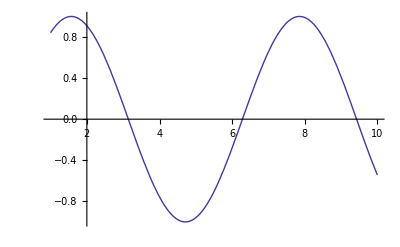

```mathematica
Plot[Sin[x],{x,1,10}]
```

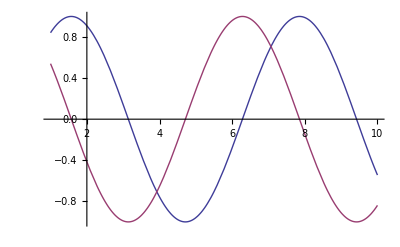

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*Symbolic Computation*)
```

```mathematica
3+62-1
```

64

```mathematica
3x-x+2
```

2+2 x

```mathematica
x^6-3x+5x+6x^6+x^2
```

2 x+x^2+7 x^6

```mathematica
(x+2y+1)(x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
sqrt[2/L]*Sin[[nπx]/L]
```

```mathematica
n!
```

```mathematica
n!
```

n!

```mathematica
(*Values for Symbols*)
```

```mathematica
1+2x/.x->3
```

7

```mathematica
1+x+x^2/.x->2y
```

1+2 y+4 y^2

```mathematica
x->3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y)(x-y)^2/.(x->3,y->1-a)
```

```mathematica
x=3
x^2-1
```

3

8

```mathematica
x=1+a
x^2-1
```

1+a

-1+(1+a)^2

```mathematica
x=.
```

```mathematica
x^2-1
```

-1+x^2

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
(*TransformingAlgebraic Expressions*)
```

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
(*Simplifying Algebraic Expressions*)
```

```mathematica
Simplify[x^2+2x+1]
```

(1+x)^2

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
simplify[%]
```

simplify[-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))]

```mathematica
Simplify[%]
```

simplify[1/(-1+x^4)]

```mathematica
FullSimplify[Gamma[1-x]Gamma[x]]
```

π Csc[π x]

```mathematica
(*Calculus*)
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}]
```

```mathematica
(-2+n) (-1+n) n x^(-3+n)
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
D[{x^2+y^2,xy},{{x,y}}]
```

{{2 x,2 y},{0,0}}

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]

```mathematica
Integrate[Ln[x],x]
```

```mathematica
∫Exp[x]ⅆx
```

ⅇ^x

```mathematica
Integrate[x^2+y^2,{x,0,1},{y,0,x}]
```

1/3

```mathematica
Integrate[x^10Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

(21 π)/512

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[xb[x]^2,b[x]]
```

b[x] xb[x]^2

```mathematica
%/.x->w
```

b[w] xb[w]^2

```mathematica
(*Differential Equations*)

DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2y'[x]+y[0]/.%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
y'[x]+y[x]==1/.%%
```

```mathematica
{True}
```

{True}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==y'[x]},{y,z},x]
```

{{y→Function[{x},C[1] Cos[x]+C[2] Sin[x]],z→Function[{x},C[2] Cos[x]-C[1] Sin[x]]}}

```mathematica
DSolve[y[x]y'[x]==1,y,x]
```

{{y→Function[{x},-√2 √(x+C[1])]},{y→Function[{x},√2 √(x+C[1])]}}

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[y''[x]-Exp[x]y[x]==0,y[x],x]
```

{{y[x]→BesselI[0,2 √(ⅇ^x)] C[1]+2 BesselK[0,2 √(ⅇ^x)] C[2]}}

```mathematica
DSolve[y'[x]-xy[x]^2-y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x ∫_1^x ⅇ^(-K[1]) xy[K[1]]^2ⅆK[1]}}

```mathematica
DSolve[y'[x]-y[x]==UnitStep[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x (1-ⅇ^-x) UnitStep[x]}}

```mathematica
(*Plotting*)
```

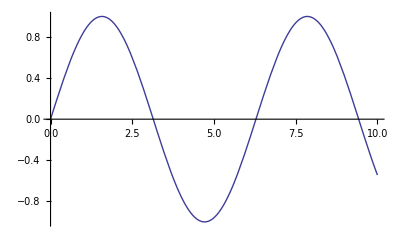

```mathematica
Plot[Sin[x],{x,0,10}]
```

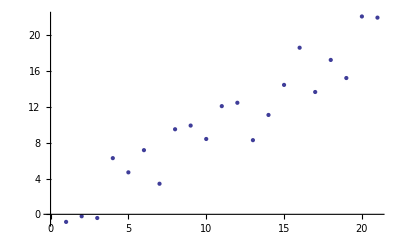

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

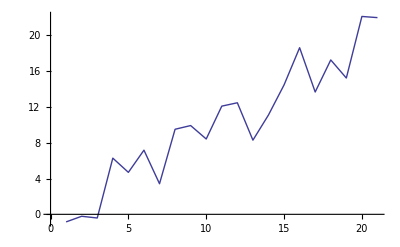

```mathematica
ListLinePlot[datapts]
```

```mathematica
Plot3D[Sin[x]Cos[y],{x,0,5},{y,0,5}]
```

-Graphics3D-

```mathematica
G
```